```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["32_cv.dat","Table"];
MagnetData = Import["32_magnetization.dat","Table"];
SusceptData = Import["32_susceptibility.dat","Table"];
```

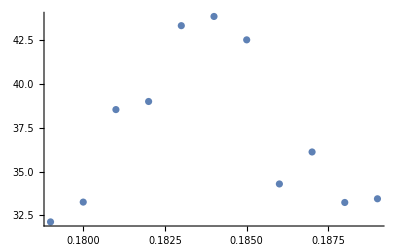

```mathematica
ListPlot[Take[SusceptData,{180,190}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{180,190}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,40},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{41.569 ⅇ^(-11445.7 (-0.183838+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 41.569 | 1.2238 | 33.9673 | 6.16493×10^-10
Sigma | 0.00660943 | 0.0007266 | 9.09637 | 0.0000171343
mu | 0.183838 | 0.000314914 | 583.77 | 8.30318×10^-20}

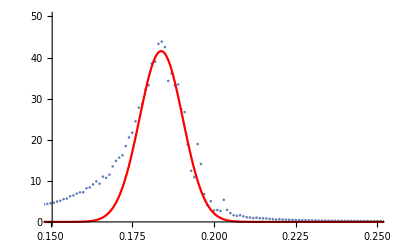

```mathematica
Show[ListPlot[SusceptData, PlotRange->{{0.15,0.25},{0,50}}],Plot[SusceptFit[x],{x,0,0.4},PlotRange->{{0,0.4},{0,500}}, PlotStyle->Red]]
```

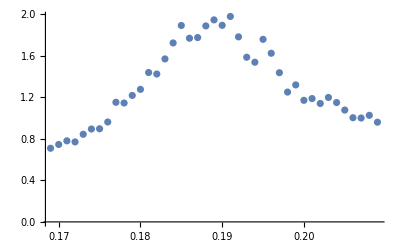

```mathematica
ListPlot[Take[CvData,{170,210}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{160,210}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{A,Sigma,mu},x]
```

FittedModel[1.70748 ⅇ^(-1965.26 (-«20»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{1.70748 ⅇ^(-1965.26 (-0.189745+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.70748 | 0.0364287 | 46.8718 | 9.64556×10^-42
Sigma | 0.0159505 | 0.000533781 | 29.8822 | 1.13292×10^-32
mu | 0.189745 | 0.000441585 | 429.69 | 1.03449×10^-87}

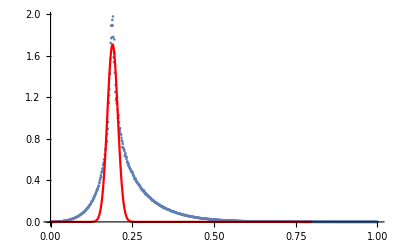

```mathematica
Show[ListPlot[CvData, PlotRange->Full],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```